# Driehoek

## Numeriek

## LCA

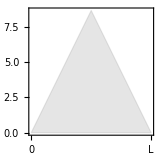

```mathematica
L=10;
n=25;
EquilateralTriangle[s_]:=Triangle[{{0,0},{s,0},{s/2,(Sqrt[3] s)/2}}]
t=EquilateralTriangle[L];
Graphics[{EdgeForm[Thin],Opacity[0.2],Gray,t}, Frame->True,FrameTicks->{{{None,None},None},{{{0,"0"},{L,"L"} },None}}, Axes->True, AxesLabel->{"x",y},AxesStyle->Thick, PlotRange->Automatic]
```

```mathematica
{vals, funs} = NDEigensystem[{-Laplacian[u[x,y],{x,y}]+NeumannValue[0, {x,y}∈ RegionBoundary[t]]}, u, {x,y} ∈ t, n];
vals
Table[Plot3D[funs[[i]][x,y], {x,y} ∈ t, PlotRange->All, PlotLabel->vals[[i]],AxesLabel->{x,y}],{i,1,n}]
```

{7.0688×10^-16,0.17546,0.17546,0.526398,0.701879,0.701884,1.22845,1.22846,1.57961,1.57963}

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

## Vervorming

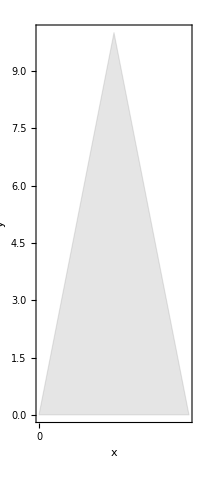

```mathematica
L = 10;
W = 1;
driehoek := Triangle[{{0,0},{W,0},{W/2,(L)}}];
Graphics[{EdgeForm[Thin],Opacity[0.2],Gray,driehoek}, Frame->True,FrameTicks->{{{None,None},None},{{{0,"0"},{L,"L"} },None}}, Axes->True, AxesLabel->{"x",y},AxesStyle->Thick, PlotRange->Automatic]
```

```mathematica
{vals, funs} = NDEigensystem[{-Laplacian[u[x,y],{x,y}]+NeumannValue[0, {x,y}∈ RegionBoundary[driehoek]]}, u, {x,y} ∈ driehoek, n];
vals
Table[Plot3D[funs[[i]][x,y], {x,y} ∈ driehoek, PlotRange->All, PlotLabel->vals[[i]],AxesLabel->{x,y}],{i,1,n}]
```

{1.88855×10^-14,0.146698,0.491775,1.03413,1.77374,2.7106,3.84473,5.17617,6.70501,8.43144,10.3554,11.4875,12.4772,14.7965,16.1142,17.3149,20.0328,20.1148,22.949,24.1013,26.0677,28.1905,29.3833,32.4118,32.906}

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
lijstje = {{0,0}, {1,0}, {2,0},{3,0}, {4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{0,1}, {11,0},{12,0} , {1,1}, {13,0},{14,1}, {2,1},{15,0},{3,1}, {16,0},  {4,1}, {17,0}, {5,1}, {18,0}}
```

{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{0,1},{11,0},{12,0},{1,1},{13,0},{14,1},{2,1},{15,0},{3,1},{16,0},{4,1},{17,0},{5,1},{18,0}}

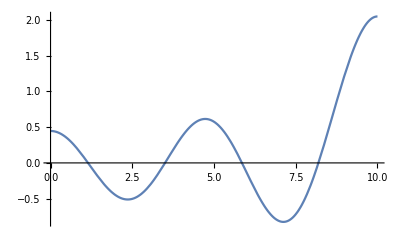

```mathematica
Plot[funs[[5]][0.5,y], {y,0,L}]
```

```mathematica
SyntaxInformation[findAllRoots]={"LocalVariables"->{"Plot",{2,2}},"ArgumentsPattern"->{_,_,OptionsPattern[]}};
SetAttributes[findAllRoots,HoldAll];

Options[findAllRoots]=Join[{"ShowPlot"->False,PlotRange->All},FilterRules[Options[Plot],Except[PlotRange]]];

findAllRoots[fn_,{l_,lmin_,lmax_},opts:OptionsPattern[]]:=Module[{pl,p,x,localFunction,brackets},localFunction=ReleaseHold[Hold[fn]/.HoldPattern[l]:>x];
If[lmin≠lmax,pl=Plot[localFunction,{x,lmin,lmax},Evaluate@FilterRules[Join[{opts},Options[findAllRoots]],Options[Plot]]];
p=Cases[pl,Line[{x__}]:>x,Infinity];
If[OptionValue["ShowPlot"],Print[Show[pl,PlotLabel->"Finding roots for this function",ImageSize->200,BaseStyle->{FontSize->8}]]],p={}];
brackets=Map[First,Select[(*This Split trick pretends that two points on the curve are "equal" if the function values have _opposite _ sign.Pairs of such sign-changes form the brackets for the subsequent FindRoot*)Split[p,Sign[Last[#2]]==-Sign[Last[#1]]&],Length[#1]==2&],{2}];
x/.Apply[FindRoot[localFunction==0,{x,##1}]&,brackets,{1}]/.x->{}]
```

{0,π/10,π/5,(3 π)/10,(2 π)/5,π/2,(3 π)/5,(7 π)/10,(4 π)/5,(9 π)/10,π,0,(11 π)/10,(6 π)/5,π/10,(13 π)/10,(7 π)/5,π/5,(3 π)/2,(3 π)/10,(8 π)/5,(2 π)/5,(17 π)/10,π/2,(9 π)/5}

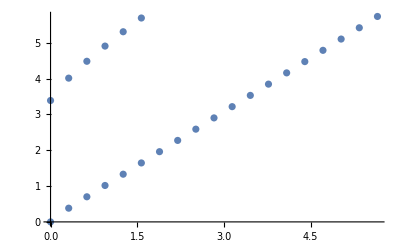

```mathematica
k = Table[Pi/L lijstje[[i,1]],{i,1,n}]
data=Transpose@{k,Sqrt[vals]};
ListPlot[data]
```

```mathematica
1/Sqrt[2Pi]  Sqrt[vals]
```

{5.48244×10^-8,0.152799,0.279765,0.405694,0.531319,0.656814,0.782245,0.907642,1.03302,1.15841,1.28379,1.35215,1.40919,1.53458,1.60146,1.66005,1.78558,1.78924,1.91114,1.95853}

```mathematica
findAllRoots[funs[[5]][0.5,y],{y,0,10}]
```

{1.1462,3.50228,5.85524,8.1943}